```mathematica
MinGen[X_] := If[FreeQ[X,Around],Min[X],Min[#["Value"]& /@ X]];
MaxGen[X_] := If[FreeQ[X,Around],Max[X],Max[#["Value"]& /@ X]]
```

```mathematica
MinVal[L_, n_]:= MinGen[Transpose[L][[n]]];
```

```mathematica
MaxVal[L_, n_]:= MaxGen[Transpose[L][[n]]];
```

```mathematica
MinGen[{Around[1,0.1],Around[3,0.2]}]
```

1.

```mathematica
MinGen[{1,0.1,3,0.2}]
```

0.1

```mathematica
MyDnSample[L_, n_] := L[[#]]& /@Range[1,Length[L],n];
```

```mathematica
DataWithErrors[data_,n_, bins_]:=Around[#[[1]],#[[2]]] &/@ Transpose[{Mean[#],StandardDeviation[#]/Sqrt[bins]}]& /@ Partition[Sort[data,#1[[n]]<#2[[n]]&],bins];
```

```mathematica
DataWithErrors[data_, bins_]:=Around[#[[1]],#[[2]]] &/@ Transpose[{Mean[#],StandardDeviation[#]/Sqrt[bins]}]& /@ Partition[data,bins];
```

```mathematica
DataWithWeights[data_, bins_]:={Mean[#],Sqrt[bins]/StandardDeviation[#]}& /@ Partition[data,bins];
```

```mathematica
Around[#[[1]],#[[2]]]& /@Transpose[{{m,m,m},{s,s,s}}]
```

{ms,ms,ms}

```mathematica
DataWithErrors[ArrayReshape[Table[RandomReal[],120],{40,3}],5]
```

{{0.580.06,0.630.16,0.650.18},{0.490.16,0.560.15,0.470.07},{0.390.13,0.620.17,0.690.10},{0.670.09,0.620.12,0.550.15},{0.430.16,0.340.09,0.580.15},{0.400.13,0.340.12,0.470.08},{0.550.15,0.560.12,0.400.09},{0.520.16,0.330.04,0.330.06}}

```mathematica
ttt=DataWithWeights[ArrayReshape[Sort[Table[RandomReal[],100]],{50,2}],5]
```

{{{0.029852,0.0348022},{126.096,122.971}},{{0.121155,0.129798},{57.8026,61.1794}},{{0.221089,0.232843},{66.2899,64.5789}},{{0.293148,0.302134},{97.767,89.8627}},{{0.399093,0.406663},{55.4271,58.2257}},{{0.512952,0.526466},{49.6835,65.1147}},{{0.668581,0.682107},{62.022,80.0482}},{{0.773288,0.783723},{49.3485,48.7425}},{{0.871459,0.878258},{83.5616,83.1165}},{{0.970348,0.977494},{89.5687,96.1052}}}

```mathematica
Transpose[ttt]
```

{{{0.029852,0.0348022},{0.121155,0.129798},{0.221089,0.232843},{0.293148,0.302134},{0.399093,0.406663},{0.512952,0.526466},{0.668581,0.682107},{0.773288,0.783723},{0.871459,0.878258},{0.970348,0.977494}},{{126.096,122.971},{57.8026,61.1794},{66.2899,64.5789},{97.767,89.8627},{55.4271,58.2257},{49.6835,65.1147},{62.022,80.0482},{49.3485,48.7425},{83.5616,83.1165},{89.5687,96.1052}}}

```mathematica
test =DataWithErrors[ArrayReshape[Sort[Table[RandomReal[],256]],{64,4}],4]
```

{{0.0210.010,0.0250.011,0.0280.012,0.0330.012},{0.1030.017,0.1130.014,0.1190.013,0.1240.014},{0.1800.012,0.1830.012,0.1880.011,0.1900.011},{0.2320.011,0.2410.016,0.2460.017,0.2490.017},{0.3180.010,0.3200.010,0.3240.010,0.3300.012},{0.3920.013,0.3980.013,0.4000.012,0.4090.010},{0.4450.004,0.4470.004,0.4490.004,0.4500.005},{0.4840.010,0.4860.010,0.4900.010,0.4950.009},{0.5450.012,0.5480.011,0.5540.010,0.5590.010},{0.5990.010,0.6030.010,0.6070.012,0.6120.013},{0.6660.008,0.6690.009,0.6740.007,0.6760.007},{0.7140.009,0.7190.010,0.7220.010,0.7240.010},{0.7670.007,0.7690.007,0.7700.007,0.7730.006},{0.8270.018,0.8310.018,0.8370.018,0.8430.017},{0.9020.009,0.9070.008,0.9080.008,0.9100.008},{0.9590.011,0.9650.011,0.9670.010,0.9720.011}}

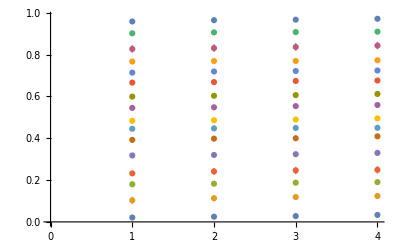

```mathematica
ListPlot[test]
```

```mathematica
ShowFitModel[data_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
Show[
ListPlot[data, PlotStyle->{dcol},PlotLegends->{Ylabel}],
Plot[model[x],{x,MinVal[data,1],MaxVal[data,1]},PlotStyle->{mcol, PointSize[0.1]},
PlotLegends->{N[model[x],7]},PlotRange->All],
PlotLabel->title,
AxesLabel->{Xlabel, Ylabel}
];
ShowLogFitModel[data_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
Show[
ListPlot[data, PlotStyle->{dcol},PlotLegends->{Ylabel}],
Plot[model[x],{x,MinVal[data,1],MaxVal[data,1]},PlotStyle->{mcol, PointSize[0.5]},
PlotLegends->{N[FullSimplify[Exp[model[Log[x]]]],7]},PlotRange->All],
PlotLabel->title,
AxesLabel->{Xlabel, Ylabel}
];
```

```mathematica
ShowLogFitModelBin[data_,bins_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
ShowLogFitModel[DataWithErrors[data,1,bins], model,Xlabel,Ylabel, title, dcol, mcol];
```

```mathematica
ClearAll[NumericalVector];
```

```mathematica
NumericalVector[{}] = False;
```

```mathematica
NumericVector[X_] := And @@(NumericQ  /@ X);
```

```mathematica
NumericVector[{1,2,3}]
```

True

```mathematica
testP0=BinaryReadList[StringJoin["/Users/am10485/Downloads/ClusterDataGPU2e8/FDBins.pos.alt.np"],"Real64"];
```

```mathematica
Length[testP0]
```

7340032

```mathematica
Length[testP0]/7
```

1048576

```mathematica
testP1 = ArrayReshape[testP0,{Length[testP0]/7,7}];
```

```mathematica
testP1[[;;10]]
```

{{79.,-35.9286,0.00186777,-13.6582,6.38964,-25.2469,6.82349},{80.,-35.9245,0.00106351,-18.3916,6.93627,-28.102,9.14357},{80.,-35.9222,0.000703541,-19.3796,5.26213,-30.4484,5.46568},{80.,-35.9182,0.00187224,-19.0867,4.36443,-30.2782,5.10183},{80.,-35.9134,0.000840053,-19.8501,6.16714,-30.6081,6.64805},{80.,-35.9108,0.000924809,-17.9403,7.20836,-29.4567,7.70247},{80.,-35.908,0.000189845,-15.9452,6.13022,-26.7995,6.73063},{80.,-35.9075,0.000163539,-20.6231,7.56741,-31.5177,9.09617},{80.,-35.9061,0.000555249,-19.4855,7.84233,-31.0325,8.57952},{80.,-35.9046,0.00059437,-20.491,7.22529,-31.6752,7.85235}}

```mathematica
testP1[[-10;;]]
```

{{80.,-2.28946,Indeterminate,-12.9861,5.65269,-23.6379,6.36038},{80.,-2.28946,Indeterminate,-12.1737,3.28293,-23.2582,4.52323},{80.,-2.28946,1.25817×10^-7,-13.2833,4.96702,-24.6466,5.40731},{80.,-2.28946,2.68242×10^-8,-12.6819,4.00526,-23.826,4.76284},{80.,-2.28946,8.04726×10^-8,-10.7075,1.26774,-22.716,3.14212},{80.,-2.28946,Indeterminate,-12.2119,1.99468,-23.0574,2.57124},{80.,-2.28946,Indeterminate,-12.9947,4.10343,-24.5565,4.46799},{80.,-2.28946,5.99807×10^-8,-10.3233,1.62476,-20.4761,3.09816},{80.,-2.28946,Indeterminate,-12.0177,2.05629,-23.6199,3.19927},{80.,-2.28946,Indeterminate,-11.2208,3.30157,-21.6829,5.53302}}

```mathematica
testP=Select[testP1,NumericVector];
```

```mathematica
Dimensions[testP]
```

{692010,7}

```mathematica
testN0=BinaryReadList[StringJoin["/Users/am10485/Downloads/ClusterDataGPU2e8/FDBins.neg.alt.np"],"Real64"];
```

```mathematica
Length[testN0]
```

7340032

```mathematica
Length[testN0]/7
```

1048576

```mathematica
testN1 = ArrayReshape[testN0,{Length[testN0]/7,7}];
```

```mathematica
testN=Select[testN1,NumericVector];
```

```mathematica
Dimensions[testN]
```

{691945,7}

```mathematica
DataAround[A_,B_]:= Around[#[[1]],#[[2]]]&/@Transpose[{A, B}];
```

```mathematica
DataAround[Range[10], Table[1,10]]
```

{1.01.0,2.01.0,3.01.0,4.01.0,5.01.0,6.01.0,7.01.0,8.01.0,9.01.0,10.01.0}

```mathematica
First /@{{1,2},{3,4}}
```

{1,3}

```mathematica
AllSamples = Join[Select[testP,#[[1]] >1&],Select[testN,#[[1]] >1&]];
```

```mathematica
Length[AllSamples]
```

1383955

```mathematica
MakeProbAllDS[samples_, name_,bins_]:=Block[{P,nums, cc,cs,dd,ds,oo,os,numtot,Tail,lint,data, weights},
{nums, cc,cs,dd,ds,oo,os} = Transpose[Sort[samples, #1[[4]] < #2[[4]]&]];
numtot = Plus@@ nums ;
data =Transpose[{dd,Log[1-Accumulate[nums]/(1+numtot)]}];
ListPlot[DataWithErrors[data,bins],PlotStyle->Red, PlotLegends->{"DS"}]
]
```

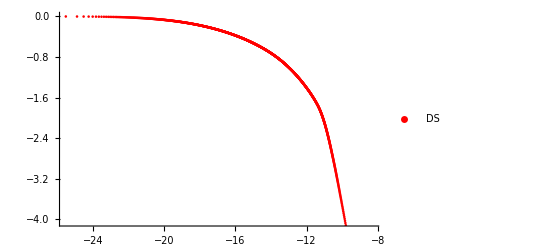

```mathematica
SHDS=MakeProbAllDS[AllSamples, "DS", 1000]
```

```mathematica
MakeProbAllOO[samples_, name_, bins_]:=Block[{P,nums, cc,cs,dd,ds,oo,os,numtot,Tail,lint,data, weights},
{nums, cc,cs,dd,ds,oo,os} = Transpose[Sort[samples, #1[[6]] < #2[[6]]&]];
numtot = Plus@@ nums ;
data =Transpose[{oo,Log[1-Accumulate[nums]/(1+numtot)]}];
ListPlot[DataWithErrors[data,bins],PlotStyle->Blue, PlotLegends->{"OO"}]
]
```

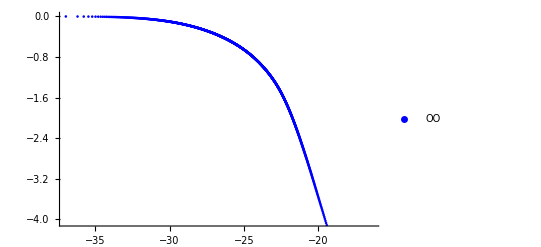

```mathematica
SHOO =MakeProbAllOO[AllSamples,"|ω.ω|",1000]
```

```mathematica
PlotOvsKAccum[samples_, bins_]:=Block[{Q,nums, dd,ds,oo,os,SP, SN,numtot,Tail,lm,data, weights},
{nums, cc,cs,dd,ds,oo,os} = Transpose[Sort[samples, #1[[6]] < #2[[6]]&]];
{data, weights}= {Transpose[{oo,Accumulate[-dd]}],nums};
ListPlot[DataWithErrors[data,bins],
PlotLabel->"Prob[-Log[ k Sqrt[ν t]];Log|ω.ω|/q^2 < y]",
AxesLabel->{"Log[|ω.ω|/q^2]","Accum[-Log[ k Sqrt[ν t]]"}]
];
```

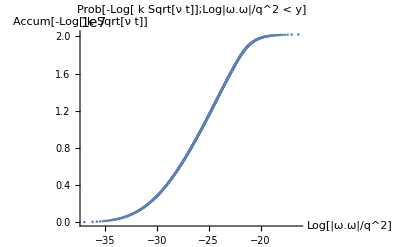

```mathematica
PlotOvsKAccum[AllSamples, 1000]
```